### Einzelmessung

```mathematica
Clear[RiV, UV, IA]
R[U_,I_] := U /(I - U/RiV)
du = D[R[UV,IA],UV ]//FullSimplify
di = D[R[UV,IA],IA] //FullSimplify
UV = 4.852;
IA = 0.07141;
RiV =10000000;
{du,di}
```

### Glühdraht

```mathematica
Clear[α,β,R0, θ0]
R[θ_] := R0(1+α(θ-θ0)+β(θ-θ0)^2)
InverseFunction[R]//FullSimplify
```

```mathematica
α = 4.1*10^(-3);
β = 1.0*10^(-6);
R0 = 30.39;
θ0 = 20;
data = {
197.6344928,
286.2022208,
342.4816085,
395.1312935,
442.0649958,
481.3619122
};
temp = Table[NSolve[R[θ]==d,θ, PositiveReals],{d,data}] // Flatten
```

### 2: AC-DC Kopplung

```mathematica
Plot[20*Log10[Abs[1/(1+7/(ⅈ*f))]],{f,1, 100},
PlotLabel->Style["Betragsspektrum des Hochpasses",FontWeight->Bold, FontSize->14],
Frame -> True,
PlotRange->{{0,100},{-3,0}},
FrameLabel->{Style["Frequenz / Hz", FontSize->14],Style[ "Dämpfung / dB", FontSize->12]},
ImageSize->Medium
]
```

### Kabelkapazität

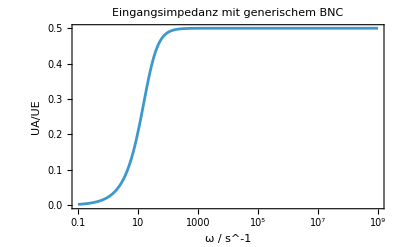

1.75647-1326.48 ⅈ

{1326.48,-89.9241}

```mathematica
Clear[T,ZA,ZE,RE,XE,XK,XAC,ω]
Par[Z1_,Z2_]:= 1/ (1/Z1+1/Z2)

ZA  =Par[ⅈ*XE,RE];
ZE = ⅈ*XAC+ZA;
Z = Par[ⅈ*XK,ZE]//FullSimplify;
T = ZA/(ZA+ZE);


RE = 1000000;
XE = -1/(ω*20*10^(-12));
XAC = -1/(ω*22.7*10^(-9));
XK = -1/(ω*100*10^(-12));

LogLinearPlot[
Abs[T],
{ω,0.1,1000000000},
Frame -> True,
FrameLabel->{"ω / s^-1", UA/UE},
PlotLabel->"Eingangsimpedanz mit generischem BNC"
]

ω=1000000*2*Pi;

Z
{Abs[Z],180*Arg[Z]/Pi}
```

### Tastkopf

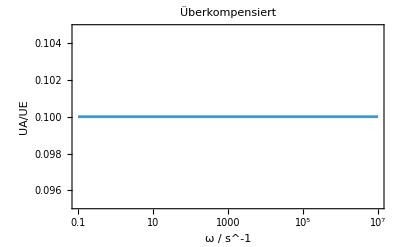

17.5905-13262.9 ⅈ

{13262.9,-89.924}

```mathematica
Clear[Z,T,ω,XT, RT, XE, RE]
ZT  = Par[-ⅈ*XT, RT];
ZE = Par[-ⅈ*XE, RE];
Z = ZT+ZE//FullSimplify;

T =ZE/Z;


CT = (40/3)*10^(-12);
RT = 9000000;
RE = 1000000;
XT = 1/(ω*CT);
XE = 1/(ω*120*10^(-12));

LogLinearPlot[
Abs[T],
{ω,0.1,10000000},
FrameLabel->{"ω / s^-1", UA/UE},
Frame->True,
PlotLabel->"Überkompensiert"
]

ω=2*Pi*1000000;
N[Z]
N[{Abs[Z],180*Arg[Z]/Pi}]
```